```mathematica
ClearAll["Global`*"]

"Growth"

runNames= {"Wigly_Cylinder", "leaves"};
paramterTypes={"ricci","mean","all","none","conformal","elastic", "uniform"};



(*runIndx =1; paramIndex =2;*)
spatialDim = 3;

numTimeSteps = 30; timeSteps = Range[numTimeSteps] -1;


fs =19;smoothing =1;

colorTheme = "GreenPinkTones";

setPlotOptions[]:=(

th = 0.005;fs=16; ps=0.01;
SetOptions[Plot, LabelStyle->Directive[FontFamily->"Myriad Pro", Black, FontSize->fs], PlotStyle-> {Blue,Thickness[th]}, PlotRange->All];
SetOptions[ListPlot, LabelStyle->Directive[FontFamily->"Myriad Pro", Black, FontSize->fs], PlotStyle-> {Blue,PointSize[ps]}, PlotRange->All];
SetOptions[ListLogPlot, LabelStyle->Directive[FontFamily->"Myriad Pro", Black, FontSize->fs], PlotStyle-> {Blue,PointSize[ps]}, PlotRange->All];
SetOptions[ListLinePlot, LabelStyle->Directive[FontFamily->"Myriad Pro", Black, FontSize->fs], PlotStyle-> {Blue,Thickness[th]}, PlotRange->All];
SetOptions[ParametricPlot, LabelStyle->Directive[FontFamily->"Myriad Pro", Black, FontSize->fs], PlotStyle-> {Blue,Thickness[th]}, PlotRange->All];
SetOptions[ListPointPlot3D, LabelStyle->Directive[FontFamily->"Myriad Pro", Black, FontSize->fs], PlotStyle-> {Blue,Thickness[th]}, PlotRange->All];
SetOptions[MatrixPlot, BaseStyle->Directive[FontFamily->"Myriad Pro", Black, FontSize->fs]];
SetOptions[BoxWhiskerChart, BaseStyle->Directive[FontFamily->"Myriad Pro", Black,Bold, FontSize->fs]];
SetOptions[DistributionChart, BaseStyle->Directive[FontFamily->"Myriad Pro", Black,Bold, FontSize->fs]];
)

setPlotOptions[];


plotDefArrows[ runIndx_, paramIndex_, isSmoothing_:False][timeIndex_]:= (

arrowScale =  0.2; arrowThickness = 0.0025;

paramterType = paramterTypes[[paramIndex]];
runName=runNames[[runIndx]];

resultDir = FileNameJoin[{NotebookDirectory[], "Run Results", runName}];
meshDir = FileNameJoin[{NotebookDirectory[], "Mesh Data", runName}];

SetDirectory[resultDir];
(*allMax =Import[paramterType <>"_MaxDilations.csv"][[1,1]];*)




 SetDirectory[FileNameJoin[{meshDir, "time" <> ToString[timeIndex]}]];
(*initVerts = Import["vertices.csv"];
verts = Transpose[Transpose[initVerts] - Mean[initVerts]];*)

faces = Round[Import["faces.csv"]] + 1;
numFaces = Dimensions[faces][[1]];


If[isSmoothing,gaussianFilter = Import["GaussianFilter.csv"];
filter=gaussianFilter, filter =IdentityMatrix[numFaces] ];

SetDirectory[resultDir];

maxDims =Import["MaxDimensions.csv"]//Flatten;

saveName = paramterType<> "_time" <> ToString[timeIndex]<>".csv";

newVerts = Import["new_verts_"<> saveName];
verts = Transpose[Transpose[newVerts] - Mean[newVerts]];

strainsRaw = Import["strains_"<> saveName];


strains =  ArrayReshape[ strainsRaw, {numFaces,spatialDim,spatialDim}];

{λ1,λ2,λ3} = Transpose[Eigenvalues/@strains];

eigVecs = (Eigenvectors /@  strains)[[;;,1]];

allMaxD = Max[Abs[λ1 + λ2]];
allMaxS = Max[Abs[λ1 - λ2]];

allMax = Max[Abs[Join[λ1- λ2, λ1 + λ2]]];

shears= Abs[(λ1 - λ2)/allMax];

dilations =0.5filter.(1 + ((λ1 + λ2)/allMax));

shearVecs = eigVecs*shears*arrowScale;


dilationTri[i_]:= {ColorData[colorTheme][dilations[[i]]],Triangle[verts[[faces[[i]]]]]};
dilationTris = dilationTri /@ Range[numFaces];

centroids = Mean /@ (verts[[#]]&/@ faces);
arrows = Line[{centroids[[#]] - shearVecs[[#]],centroids[[#]] + shearVecs[[#]] }&/@Range[numFaces]];


plotRegion = Cuboid[-1.2/2 maxDims,1.2/2 maxDims];

leafViewP = {-0.354, 0.334, 0.873};

g1 = Graphics3D[{EdgeForm[None], dilationTris,Yellow, Thickness[arrowThickness],arrows, White, Opacity[0],plotRegion}, PlotRange->All, BoxRatios->Automatic, Boxed->False, ViewPoint->leafViewP(*, PlotLabel->"Dilation_" <>runName <> "_time" <> ToString[timeIndex]*)]


)


plotKCurvature[ runIndx_, paramIndex_, isSmoothing_:False][timeIndex_]:= (

paramterType = paramterTypes[[paramIndex]];
runName=runNames[[runIndx]];

resultDir = FileNameJoin[{NotebookDirectory[], "Run Results", runName}];
meshDir = FileNameJoin[{NotebookDirectory[], "Mesh Data", runName}];


 SetDirectory[FileNameJoin[{meshDir, "time" <> ToString[timeIndex]}]];
(*initVerts = Import["vertices.csv"];
verts = Transpose[Transpose[initVerts] - Mean[initVerts]];*)

faces = Round[Import["faces.csv"]] + 1;
numFaces = Dimensions[faces][[1]];


(*meanCurvature = Import["Cmean.csv"]//Flatten;
gaussCurvature = Import["Cgaussian.csv"]//Flatten;*)

curvatureRaw =Import["Cgaussian.csv"]//Flatten;

If[isSmoothing,gaussianFilter = Import["GaussianFilter.csv"];
filter=gaussianFilter, filter =IdentityMatrix[numFaces] ];

SetDirectory[resultDir];

maxDims =Import["MaxDimensions.csv"]//Flatten;

saveName = paramterType<> "_time" <> ToString[timeIndex]<>".csv";

newVerts = Import["new_verts_"<> saveName];
verts = Transpose[Transpose[newVerts] - Mean[newVerts]];

κMax= Max[curvatureRaw];

curvature =0.5filter.(1 + curvatureRaw/κMax);



dilationTri[i_]:= {ColorData[colorTheme][curvature[[i]]],Triangle[verts[[faces[[i]]]]]};
dilationTris = dilationTri /@ Range[numFaces];


plotRegion = Cuboid[-1.2/2 maxDims,1.2/2 maxDims];

leafViewP = {-0.354, 0.334, 0.873};

g1 = Graphics3D[{EdgeForm[None], dilationTris, White, Opacity[0],plotRegion}, PlotRange->All, BoxRatios->Automatic, Boxed->False, ViewPoint->leafViewP(*, PlotLabel->"Dilation_" <>runName <> "_time" <> ToString[timeIndex]*)]


)


plotHCurvature[ runIndx_, paramIndex_, isSmoothing_:False][timeIndex_]:= (

paramterType = paramterTypes[[paramIndex]];
runName=runNames[[runIndx]];

resultDir = FileNameJoin[{NotebookDirectory[], "Run Results", runName}];
meshDir = FileNameJoin[{NotebookDirectory[], "Mesh Data", runName}];


 SetDirectory[FileNameJoin[{meshDir, "time" <> ToString[timeIndex]}]];
(*initVerts = Import["vertices.csv"];
verts = Transpose[Transpose[initVerts] - Mean[initVerts]];*)

faces = Round[Import["faces.csv"]] + 1;
numFaces = Dimensions[faces][[1]];


(*meanCurvature = Import["Cmean.csv"]//Flatten;
gaussCurvature = Import["Cgaussian.csv"]//Flatten;*)

curvatureRaw =Import["Cmean.csv"]//Flatten;

If[isSmoothing,gaussianFilter = Import["GaussianFilter.csv"];
filter=gaussianFilter, filter =IdentityMatrix[numFaces] ];

SetDirectory[resultDir];

maxDims =Import["MaxDimensions.csv"]//Flatten;

saveName = paramterType<> "_time" <> ToString[timeIndex]<>".csv";

newVerts = Import["new_verts_"<> saveName];
verts = Transpose[Transpose[newVerts] - Mean[newVerts]];

κMax= Max[curvatureRaw];

curvature =0.5filter.(1 + curvatureRaw/κMax);



dilationTri[i_]:= {ColorData[colorTheme][curvature[[i]]],Triangle[verts[[faces[[i]]]]]};
dilationTris = dilationTri /@ Range[numFaces];


plotRegion = Cuboid[-1.2/2 maxDims,1.2/2 maxDims];

leafViewP = {-0.354, 0.334, 0.873};

g1 = Graphics3D[{EdgeForm[None], dilationTris, White, Opacity[0],plotRegion}, PlotRange->All, BoxRatios->Automatic, Boxed->False, ViewPoint->leafViewP(*, PlotLabel->"Dilation_" <>runName <> "_time" <> ToString[timeIndex]*)]


)


plotDefVsCurvature[ runIndx_, paramIndex_, color_:Blue, isSmoothing_:False ][timeIndex_]:= (
paramterType = paramterTypes[[paramIndex]];
runName=runNames[[runIndx]];

resultDir = FileNameJoin[{NotebookDirectory[], "Run Results", runName}];
meshDir = FileNameJoin[{NotebookDirectory[], "Mesh Data", runName}];


 SetDirectory[FileNameJoin[{meshDir, "time" <> ToString[timeIndex]}]];
(*gaussianFilter = Import["GaussianFilter.csv"];*)
meanCurvature = Import["Cmean.csv"]//Flatten;
gaussCurvature = Import["Cgaussian.csv"]//Flatten;



SetDirectory[resultDir];
strainsRaw = Import["strains_"<> paramterType<> "_time" <> ToString[timeIndex]<>".csv"];
numFaces = Length[strainsRaw];

(*If[isSmoothing,filter=gaussianFilter, filter =IdentityMatrix[numFaces] ];*)
filter =IdentityMatrix[numFaces];
strains =  ArrayReshape[ filter.strainsRaw, {numFaces,spatialDim,spatialDim}];

dilations = Tr /@ strains;

nDilations = dilations/Max[Abs[dilations]];
(*FrameTicks->{{{-1,0,1},None},{{0,Pi,2 Pi,3 Pi},None}}*)

label = Directive[FontFamily->"Myriad Pro", Black, FontSize->fs ];
g1 = ListPlot[{meanCurvature^2,nDilations }//Transpose, AxesLabel->{"H^2", "D̃"},  PlotRange->All, PlotTheme->"SolidGrid", LabelStyle->label, AxesOrigin->{0,0},PlotStyle->{PointSize[0.012], color}];
g2 = ListPlot[{gaussCurvature,nDilations }//Transpose, AxesLabel->{"K", "D̃"},  PlotRange->All, PlotTheme->"SolidGrid", LabelStyle->label, AxesOrigin->{0,0}, PlotStyle->{PointSize[0.012], color}];

{g1,g2}
)


κDefCorrelation[ runIndx_, paramIndex_][timeIndex_]:= (
paramterType = paramterTypes[[paramIndex]];
runName=runNames[[runIndx]];

resultDir = FileNameJoin[{NotebookDirectory[], "Run Results", runName}];
meshDir = FileNameJoin[{NotebookDirectory[], "Mesh Data", runName}];


 SetDirectory[FileNameJoin[{meshDir, "time" <> ToString[timeIndex]}]];
(*gaussianFilter = Import["GaussianFilter.csv"];*)
meanCurvature = Import["Cmean.csv"]//Flatten;
gaussCurvature = Import["Cgaussian.csv"]//Flatten;



SetDirectory[resultDir];
strainsRaw = Import["strains_"<> paramterType<> "_time" <> ToString[timeIndex]<>".csv"];
numFaces = Length[strainsRaw];


strains =  ArrayReshape[ strainsRaw, {numFaces,spatialDim,spatialDim}];

dilations = Tr /@ strains;

nDilations = dilations/Max[Abs[dilations]];

lm1= LinearModelFit[{gaussCurvature, nDilations}//Transpose, {1,x},x];
lm2= LinearModelFit[{meanCurvature^2, nDilations}//Transpose, {1,x},x];

{Mean[Abs[lm1["FitResiduals"]/(Max[nDilations] - Min[nDilations])]], Mean[Abs[lm2["FitResiduals"]/(Max[nDilations] - Min[nDilations])]], Correlation[gaussCurvature, nDilations]}

)



residualPlotK[runIndx_,paramIndex_, color_:Orange]:= (

redis = LowpassFilter[κDefCorrelation[runIndx,paramIndex][#][[3]]&/@timeSteps, smoothing];


times  = timeSteps/numTimeSteps; residData = Transpose[{times, redis}];

label = Directive[FontFamily->"Myriad Pro", Black, FontSize->fs ];

ListLinePlot[residData , PlotStyle->{Thick, color}, PlotRange->All, PlotTheme->"SolidGrid", LabelStyle->label, AxesOrigin->{0,0}]

)

residualPlotH[runIndx_,paramIndex_, color_:Orange]:= (

redis = LowpassFilter[κDefCorrelation[runIndx,paramIndex][#][[2]]&/@timeSteps, smoothing];


times  = timeSteps/numTimeSteps; residData = Transpose[{times, redis}];

label = Directive[FontFamily->"Myriad Pro", Black, FontSize->fs ];

ListLinePlot[residData , PlotStyle->{Thick, color}, PlotRange->All, PlotTheme->"SolidGrid", LabelStyle->label, AxesOrigin->{0,0}]

)


plotGrowthDefs[ runIndx_, paramIndex_, isSmoothing_:True][timeIndex_]:= (

paramterType = paramterTypes[[paramIndex]];
runName=runNames[[runIndx]];

resultDir = FileNameJoin[{NotebookDirectory[], "Run Results", runName}];
meshDir = FileNameJoin[{NotebookDirectory[], "Mesh Data", runName, "time" <> ToString[timeIndex]}];


SetDirectory[meshDir];
initVerts = Import["vertices.csv"];
verts =  Transpose[Transpose[initVerts] - Mean[initVerts]];

faces = Round[Import["faces.csv"]] + 1;
numFaces = Dimensions[faces][[1]];

If[isSmoothing,filter= Import["GaussianFilter.csv"], filter =IdentityMatrix[numFaces] ];


SetDirectory[resultDir];

maxDims =Import["MaxDimensions.csv"]//Flatten;

growthStrainsRaw = Import["growth_strains_"<> paramterType<> "_time" <> ToString[timeIndex]<>".csv"];

strainsRaw = Import["strains_"<> paramterType<> "_time" <> ToString[timeIndex]<>".csv"];

gStrains =  ArrayReshape[ growthStrainsRaw, {numFaces,spatialDim,spatialDim}];

strains =  ArrayReshape[ strainsRaw, {numFaces,spatialDim,spatialDim}];

gStrainMags = ( 2 Tr[#.#] +Tr[#]^2)& /@ gStrains; 
strainMags = ( 2 Tr[#.#] +Tr[#]^2)& /@ strains; 


 
mags=0.5 + filter.Sqrt[gStrainMags/strainMags];




magTri[i_]:= {ColorData[colorTheme][mags[[i]]],Triangle[verts[[faces[[i]]]]]};
magsTris = magTri /@ Range[numFaces];



plotRegion = Cuboid[-1.2/2 maxDims 1.2/2 maxDims];


g1 = Graphics3D[{EdgeForm[None], magsTris(*, White, Opacity[0],plotRegion*)}, PlotRange->All, BoxRatios->Automatic, Boxed->False(*, PlotLabel->"Dilation_" <>runName <> "_time" <> ToString[timeIndex]*)]


)


getMaxDeformations[ runIndx_, paramIndex_][timeIndex_]:=(
paramterType = paramterTypes[[paramIndex]];
runName=runNames[[runIndx]];

resultDir = FileNameJoin[{NotebookDirectory[], "Run Results", runName}];
SetDirectory[resultDir];

strainsRaw = Import["strains_"<> paramterType<> "_time" <> ToString[timeIndex]<>".csv"];
numFaces = Length[strainsRaw];

strains =  ArrayReshape[ strainsRaw, {numFaces,spatialDim,spatialDim}];

{λ1,λ2,λ3} = Transpose[Eigenvalues/@strains];


Max/@{Abs[λ1+ λ2],Abs[λ1- λ2]}
)



plotMaxDeformations[ runIndx_, paramIndex_]:= (


{maxD, maxS} = LowpassFilter[#, smoothing]&/@Transpose[getMaxDeformations[ runIndx, paramIndex] /@ timeSteps];

times  = timeSteps/numTimeSteps;

label = Directive[FontFamily->"Myriad Pro", Black(*, FontSize->fs *)];

ListLinePlot[{Transpose[{times, maxD}], Transpose[{times, maxS}]} , PlotStyle->{{Thick,Green},{Thick, Orange}}, PlotRange->All, PlotTheme->"SolidGrid", LabelStyle->label]
)



getMeanDeformations[ runIndx_, paramIndex_][timeIndex_]:=(
paramterType = paramterTypes[[paramIndex]];
runName=runNames[[runIndx]];

resultDir = FileNameJoin[{NotebookDirectory[], "Run Results", runName}];
SetDirectory[resultDir];

strainsRaw = Import["strains_"<> paramterType<> "_time" <> ToString[timeIndex]<>".csv"];
numFaces = Length[strainsRaw];

strains =  ArrayReshape[ strainsRaw, {numFaces,spatialDim,spatialDim}];

{λ1,λ2,λ3} = Transpose[Eigenvalues/@strains];

Mean/@{Abs[λ1+ λ2],Abs[λ1- λ2]}
)


plotMeanDeformations[ runIndx_, paramIndex_]:= (

{meanD, meanS} = LowpassFilter[#, smoothing]&/@Transpose[getMeanDeformations[ runIndx, paramIndex] /@ timeSteps];

times  = timeSteps/numTimeSteps;

label = Directive[FontFamily->"Myriad Pro", Black(*, FontSize->fs *)];

ListLinePlot[{Transpose[{times, meanD}], Transpose[{times, meanS}]} , PlotStyle->{{Thick,Green},{Thick, Orange}}, PlotRange->All, PlotTheme->"SolidGrid", LabelStyle->label]
)


getArea[runIndx_][timeIndex_]:= (
runName=runNames[[runIndx]];

meshDir = FileNameJoin[{NotebookDirectory[], "Mesh Data", runName, "time" <> ToString[timeIndex]}];
SetDirectory[meshDir];

areas = Import["faceAreas.csv"]//Flatten;

Total[areas]
)


goodnessOfFit[ runIndx_, paramIndex_][timeIndex_]:= (
paramterType = paramterTypes[[paramIndex]];
runName=runNames[[runIndx]];

resultDir = FileNameJoin[{NotebookDirectory[], "Run Results", runName}];

SetDirectory[resultDir];

growthStrainsRaw = Import["growth_strains_"<> paramterType<> "_time" <> ToString[timeIndex]<>".csv"];
numFaces = Length[growthStrainsRaw];
gStrains =  ArrayReshape[ growthStrainsRaw, {numFaces,spatialDim,spatialDim}];
gStrainMags = (Tr[#.#] + 0 0.5 Tr[#]^2)& /@ gStrains; 



(*initGStrainsRaw = Import["growth_init_strains_"<> paramterType<> "_time" <> ToString[timeIndex]<>".csv"];
initGStrains =  ArrayReshape[ initGStrainsRaw, {numFaces,spatialDim,spatialDim}];
initGStrainMags= (Tr[#.#] +Tr[#]^2)& /@ initGStrains; *)

(*SetDirectory[resultDir];
strainsRaw = Import["strains_"<> "elastic"<> "_time" <> ToString[timeIndex]<>".csv"];
strains =  ArrayReshape[ strainsRaw, {numFaces,spatialDim,spatialDim}];
strainMags = (0.5Tr[#.#] +Tr[#]^2)& /@ strains; *)



areas = getArea[runIndx][timeIndex];

initArea = Total[getArea[runIndx][0]];

goodness = 1/initArea areas.gStrainMags

)


PlotGoodnessOfFit[ runIndx_, paramIndex_, color_:Pink]:=(
gness = LowpassFilter[goodnessOfFit[ runIndx, paramIndex] /@ timeSteps, smoothing];


times  = timeSteps/numTimeSteps; data = Transpose[{times, gness}];

label = Directive[FontFamily->"Myriad Pro", Black, FontSize->fs ];

ListLinePlot[data , PlotStyle->{Thick,color}, PlotRange->All, PlotTheme->"SolidGrid", LabelStyle->label, AxesOrigin->{0,0}]
)


getGrowthParams[ runIndx_, paramIndex_:1][timeIndex_]:= (

paramterType = paramterTypes[[paramIndex]];
runName=runNames[[runIndx]];

resultDir = FileNameJoin[{NotebookDirectory[], "Run Results", runName}];
SetDirectory[resultDir];
Import["growthParameters_" <> paramterType<> "_time" <> ToString[timeIndex]<>".csv"]//Flatten
)





getInitArea[runIndx_]:= (
runName=runNames[[runIndx]];

meshDir = FileNameJoin[{NotebookDirectory[], "Mesh Data", runName, "time0"}];
SetDirectory[meshDir];

areas = Import["faceAreas.csv"]//Flatten;

Total[areas]
)


getInitGaussK[runIndx_][timeIndex_]:= (
runName=runNames[[runIndx]];

meshDir = FileNameJoin[{NotebookDirectory[], "Mesh Data", runName, "time" <> ToString[timeIndex]}];
SetDirectory[meshDir];

gaussC = Import["Cgaussian.csv"]//Flatten;

Max[Abs[gaussC]]
)

getInitMeanK[runIndx_][timeIndex_]:= (
runName=runNames[[runIndx]];

meshDir = FileNameJoin[{NotebookDirectory[], "Mesh Data", runName, "time" <> ToString[timeIndex]}];
SetDirectory[meshDir];

meanC = Import["Cmean.csv"]//Flatten;

Mean[meanC^2]
)



compareNormalDisps[ runIndx_, paramIndex_][timeIndex_]:= (

paramterType = paramterTypes[[paramIndex]];
runName=runNames[[runIndx]];

resultDir = FileNameJoin[{NotebookDirectory[], "Run Results", runName}];
meshDir = FileNameJoin[{NotebookDirectory[], "Mesh Data", runName, "time" <> ToString[timeIndex]}];

 SetDirectory[meshDir];
initVerts = Import["vertices.csv"];
deformedVerts = Import["normal_deformed_intersection.csv"];
normalVecs = Import["normal.csv"];

initNormalDisps =( deformedVerts[[#]] - initVerts[[#]]).normalVecs[[#]]&/@ Range[Length[initVerts]];

SetDirectory[resultDir];
newVerts = Import["new_verts_"<> paramterType<> "_time" <> ToString[timeIndex]<>".csv"];

normalDisps =(newVerts[[#]] - initVerts[[#]]).normalVecs[[#]]&/@ Range[Length[initVerts]];

normalDeviation =Abs[ normalDisps - initNormalDisps];

Mean[normalDeviation/Mean[Abs[initNormalDisps]]]
)
```

Growth

```mathematica
runIndx =1;
compareNormalDisps[runIndx,4]/@timeSteps
```

{0.0102469,0.0103187,0.0105945,0.0108029,0.0110367,0.0112869,0.011452,0.0116666,0.0120798,0.0122777,0.012542,0.0129367,0.0132047,0.0135607,0.0138635,0.0142293,0.014758,0.0150908,0.0154532,0.0158486,0.0162584,0.0166929,0.0171478,0.017694,0.0181254,0.0185886,0.0191447,0.0196795,0.0202131,0.020841}

```mathematica
runIndx =1;

dashed1 = Plot[1, {x,0,1}, PlotStyle->{Gray, Dashed}];
ricciGoodness = PlotGoodnessOfFit[runIndx,1]; 
meanGoodness = PlotGoodnessOfFit[runIndx,2, Orange]; 
allGoodness = PlotGoodnessOfFit[runIndx,3, Black];
noneGoodness = PlotGoodnessOfFit[runIndx,4, Purple];
Show[ricciGoodness,meanGoodness,allGoodness,noneGoodness(*, dashed1*), PlotRange->All]
```

-Graphics-

```mathematica
runIndx =2;

dashed1 = Plot[1, {x,0,1}, PlotStyle->{Gray, Dashed}];
ricciGoodness = PlotGoodnessOfFit[runIndx,1]; 
meanGoodness = PlotGoodnessOfFit[runIndx,2, Orange]; 
allGoodness = PlotGoodnessOfFit[runIndx,3, Black];
noneGoodness = PlotGoodnessOfFit[runIndx,4, Purple];
Show[(*ricciGoodness,meanGoodness,*)allGoodness,noneGoodness(*, dashed1*), PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
runIndx=1;
Show[residualPlotK[runIndx,3, Black], residualPlotK[runIndx,4,Purple], residualPlotK[runIndx,7,Blue], PlotRange->All]
```

-Graphics-

```mathematica
runIndx=2;
Show[residualPlotK[runIndx,3, Black], residualPlotK[runIndx,4,Purple], residualPlotK[runIndx,7,Blue], PlotRange->All]
```

-Graphics-

```mathematica
Plot[Sin[x],{x,0,10},Frame->True,]
```

```mathematica
runIndx =1;
Show[plotDefVsCurvature[runIndx,3, Black][15][[2]], plotDefVsCurvature[runIndx,4, Purple][15][[2]], plotDefVsCurvature[runIndx,7, Blue][15][[2]], PlotRange->All]
```

-Graphics-

```mathematica
runIndx =2;
Show[plotDefVsCurvature[runIndx,3, Black][15][[2]], plotDefVsCurvature[runIndx,4, Purple][15][[2]], plotDefVsCurvature[runIndx,7, Blue][15][[2]], PlotRange->All]
```

-Graphics-

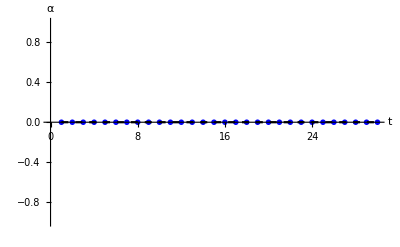
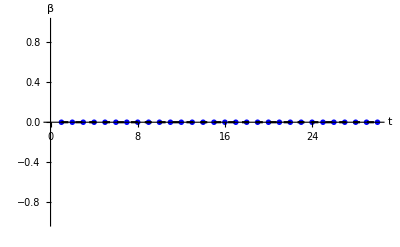
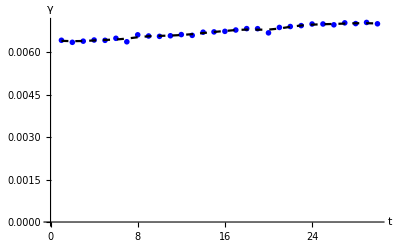

0.00672486798177172242

-Graphics-

```mathematica
runIndx =1;   paramIndx =1; smoothing = 1;
{αs, βs,γs}= Transpose[getGrowthParams[runIndx, paramIndx][#]&/@timeSteps];mα = 1(*Max[Abs[Join[αs,βs,γs]]]*);



gps ={Show[ListPlot[αs/mα, AxesLabel->{"t", "α"},  AxesOrigin->{0,0}], ListLinePlot[LowpassFilter[αs/mα,smoothing],PlotStyle->{Black, Dashed}]],
Show[ListPlot[βs/mα, AxesLabel->{"t", "β"},PlotRange->All,  AxesOrigin->{0,0}], ListLinePlot[LowpassFilter[βs/mα,smoothing],PlotStyle->{Black, Dashed}]],
Show[ListPlot[ γs/mα, AxesLabel->{"t", "γ"},  AxesOrigin->{0,0}], ListLinePlot[LowpassFilter[γs/mα,smoothing],PlotStyle->{Black, Dashed}]]}


Mean[γs]


times = timeSteps/(numTimeSteps -1);

label = Directive[FontFamily->"Myriad Pro", Black, FontSize->fs ];


γs *=(getInitGaussK[runIndx][29]) getInitArea[runIndx];

βs *=(getInitMeanK[runIndx][29]) getInitArea[runIndx];

ListLinePlot[{Transpose[{times, LowpassFilter[αs/mα,smoothing]}],Transpose[{times, LowpassFilter[βs/mα,smoothing]}],Transpose[{times, LowpassFilter[γs/mα,smoothing]}]}, PlotStyle->{{Thick,Green},{Thick,Orange},{Thick, Pink}}, PlotRange->All, PlotTheme->"SolidGrid", LabelStyle->label]
```

```mathematica
runIndx = 2
gRowStrain= GraphicsRow[{plotDefArrows[2,3][0], plotDefArrows[2,3][15], plotDefArrows[2,3][29]}]

figDir =FileNameJoin[{ParentDirectory[NotebookDirectory[]], "Figures"}];
SetDirectory[figDir]

Export[runNames[[runIndx]]  <> "_growth.pdf", gRowStrain, ImageResolution->3000];
```

2

-Graphics-

```mathematica
{plotDefArrows[2,3, False][0], plotDefArrows[2,3, True][0]}
```

{-Graphics3D-,-Graphics3D-}

```mathematica
plotCurvature[2,3, False][0]
```

-Graphics3D-

```mathematica
gRowK=  GraphicsRow[{plotKCurvature[2,3, False][0], plotKCurvature[2,3, False][15], plotKCurvature[2,3, False][29]}]

gRowH=  GraphicsRow[{plotHCurvature[2,3, False][0], plotHCurvature[2,3, False][15], plotHCurvature[2,3, False][29]}]

gRowS=  GraphicsRow[{plotDefArrows[2,3, False][0], plotDefArrows[2,3, False][15], plotDefArrows[2,3, False][29]}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
{plotDefArrows[2,1, False][0], plotDefArrows[2,1, False][15], plotDefArrows[2,1, False][29]}
{plotDefArrows[2,2, False][0], plotDefArrows[2,2, False][15], plotDefArrows[2,2, False][29]}
{plotDefArrows[2,3, False][0], plotDefArrows[2,3, False][15], plotDefArrows[2,3, False][29]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
runIndx =2;

plotDefsVSκ[runIndx_][timeIndx_]:=(
{Show[plotDefVsCurvature[runIndx,3, Black][timeIndx][[1]], plotDefVsCurvature[runIndx,4, Purple][timeIndx][[1]], plotDefVsCurvature[runIndx,7, Blue][timeIndx][[1]], PlotRange->All],
Show[plotDefVsCurvature[runIndx,3, Black][timeIndx][[2]], plotDefVsCurvature[runIndx,4, Purple][timeIndx][[2]], plotDefVsCurvature[runIndx,7, Blue][timeIndx][[2]], PlotRange->All]}

)


plotDefsVSκ[2]/@timeSteps
```

```mathematica
getArea[1][0]
```

38.0432

```mathematica
0.008348452308890291 30/(getArea[1][0])
```

0.0065834

```mathematica
6/Sqrt[getArea[1][0]]
```

0.972776

```mathematica
.
```

```mathematica
(0.0069472193669243657391`18.841811012468806 -0.00672486798177172242353333333333333333`18.827683762971724)/0.006583403827074728
```

0.0337745

```mathematica
Mean[αs]
```

0.0425775212320936897

```mathematica
Mean[βs]
```

-0.0204287